# クラスタ構造における指標

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

## 非階層クラスタ構造親和性指標

クラスタA、クラスタB間の類似度を(0,1]で示す。
a∈A、b∈B、A≡Bであり、An⊂A;(n=1,2,3,...)、Bm⊂B;(m=1,2,3,...)であるとき、
Sim({An},{Bm})を親和性指標とし、以下で定義する:

Sim({An},{Bm}) = Σ_(n,m) (|{_(An∩Bm)}|)/(|{An∪Bm}|) / √(n m)

```mathematica
intersectionNum[x___]:=Length[Intersection[x]];
```

```mathematica
unionNum[x___]:=Length[Union[x]];
```

```mathematica
clusterInner[cl1_List,cl2_List]:=Tr[Flatten[((Outer[intersectionNum,cl1,cl2,1]//N)/Outer[unionNum,cl1,cl2,1])]];
```

```mathematica
clusterAffinity[cl1_List,cl2_List]:=clusterInner[cl1,cl2]^2/Length[cl1]/Length[cl2];
```

```mathematica
clusterAffinitySq[cl1_List,cl2_List]:=clusterInner[cl1,cl2]/Sqrt[(Length[cl1]*Length[cl2])];
```

```mathematica
clusterInnerSq2[cl1_List,cl2_List]:=Tr[Flatten[((Outer[intersectionNum,cl1,cl2,1]//N)/Outer[unionNum,cl1,cl2,1])^2]];
```

```mathematica
clusterAffinitySq2[cl1_List,cl2_List]:=clusterInnerSq2[cl1,cl2]^2/(Length[cl1]*Length[cl2]);
```

```mathematica
(*clusterAffinitySq2[cl1_List,cl2_List]:=clusterInnerSq2[cl1,cl2]/Sqrt[(Length[cl1]*Length[cl2])];*)
```

```mathematica
clusterAffinitySq[{{4,5},{3},{1,2}},{{4,5},{1,2,3}}]
```

0.816497

```mathematica
clusterAffinitySq2[{{4,5},{3},{1,2}},{{4,5},{1,2,3}}]
```

0.403292

```mathematica
clusterAffinity[{{4,5},{3},{1,2}},{{4,5},{1,2,3}}]
```

0.666667

```mathematica
Sqrt[0.666666666]
```

0.816497

```mathematica
EuclideanDistance[{1},{2}]
```

1

```mathematica
Mean[{1}]
```

1

## 非階層クラスタ構造適正性指標

クラスタが適切に分割されているかを判定する指標のひとつ。
クラスタ平均半径とクラスタ数双方に対してペナルティを与えることにより、クラスタ数がN(=サンプル数)および1で適正が高くなることを防ぐことができきる指標 a を定義する。

```mathematica
averageDist[l_]:=Mean[Map[EuclideanDistance[#,Mean[l]]&,l]]
```

指標1.1 (Within Cluster Score: WCS)

N: クラスタ数
R: 全サンプルの重心からの平均距離
Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
であるとき、非階層クラスタ構造適正性指標を以下の様に定義する:

N^R · Π_n Cn^rn

N · Π_n Cn^(rn / R)

上記指標は値が小さいほど適正性が高く、最小値は1である。

```mathematica
clusteringAdequation[cl_]:=Tr[Map[Length[#]^averageDist[#]&,cl],Times]*Length[cl]^averageDist[Flatten[cl,1]]
```

```mathematica
clusteringAdequationS[cl_]:=Tr[Map[Length[#]^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl],Times]*Length[cl]
```

指標1.2 (Between Cluster Score: BCS)

N : クラスタ数
R : 全サンプルの重心から全サンプルまでの平均距離
dn : 各クラスタ中心から全サンプル中心までの平均距離
であるとき、非階層クラスタ構造適正性指標を以下の様に定義する :

1/N N^(dn / R)

上記指標は値が大きいほど適正性が高く、最大値はInfinityである。これは、WCDの考え方をクラスタセンターに応用したものである。Nは上位クラスタの数であり、すなわち1である。ただし、値は大きいほど適正性が高い。

```mathematica
clusteringAdequationD[cl_]:=(1/Length[cl])*Length[cl]^Mean[Map[(EuclideanDistance[Mean[#],Mean[Flatten[cl,1]]]/averageDist[Flatten[cl,1]])&,cl]]
```

指標1.3  (Weighted Between Cluster Score: BCSw)

R : 全サンプルの重心から全サンプルまでの平均距離
Cn : 各クラスタのメンバー数
dn : 各クラスタ中心から全サンプル中心までの距離
であるとき、非階層クラスタ構造適正性指標を以下の様に定義する :

Π_n Cn^(dn / R)

```mathematica
clusteringAdequationDw[cl_]:=Tr[Map[Length[#]^(EuclideanDistance[Mean[#],Mean[Flatten[cl,1]]]/averageDist[Flatten[cl,1]])&,cl],Times]
```

指標2

Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

Σ_n Cn^rn

上記指標は値が小さいほど適正性が高く、最小値は1である。

```mathematica
clusteringAdequation2[cl_]:=Tr[Map[Length[#]^averageDist[#]&,cl]]
```

指標3

Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
R: 全サンプルの重心からの平均距離
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

Σ_n Cn^(rn / R)

上記指標は値が小さいほど適正性が高く、最小値は1である。

```mathematica
clusteringAdequationS2[cl_]:=Tr[Map[Length[#]^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl]]
```

指標4

Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
D: サンプルの次元
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

Σ_n Cn^(rn/D)

上記指標は値が小さいほど適正性が高く、最小値は1である。

```mathematica
clusteringAdequation4[cl_,d_]:=Tr[Map[Length[#]^(averageDist[#]/d)&,cl]]
```

指標5

Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
D: サンプルの次元
R: 全サンプルの重心からの平均距離
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

Σ_n Cn^(rn/D/R)

上記指標は値が小さいほど適正性が高く、最小値は1である。

```mathematica
clusteringAdequation5[cl_,d_]:=Tr[Map[Length[#]^(averageDist[#]/d / averageDist[Flatten[cl,1]])&,cl]]
```

指標6

N: クラスタ数
R: 全サンプルの重心からの平均距離
Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
d: 全サンプルのセントロイドから各クラスタのセントロイドまでの平均距離
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

N^(d/R) · Π_n Cn^(rn / R)

```mathematica
clusteringAdequation6[cl_]:=Tr[Map[Length[#]^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl],Times]*Length[cl]^(averageDist[Map[Mean[#]&,cl]]/averageDist[Flatten[cl,1]])
```

指標7(テスト)

N: クラスタ数
R: 全サンプルの重心からの平均距離
Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
d: 全サンプルのセントロイドから各クラスタのセントロイドまでの平均距離
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

N^(R/d) · Π_n Cn^(rn / R)

指標8(テスト)

N: クラスタ数
R: 全サンプルの重心からの平均距離
Cn: 各クラスタのメンバー数
rn: 各クラスタにおける平均半径
d: 全サンプルのセントロイドから各クラスタのセントロイドまでの平均距離
であるとき、非階層クラスタ構造適正性指標aを以下の様に定義する:

N^(R-d) · Π_n Cn^(rn / R)

```mathematica
clusteringAdequation7[cl_]:=Tr[Map[Length[#]^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl],Times]*Length[cl]^(averageDist[Flatten[cl,1]]/averageDist[Map[Mean[#]&,cl]])
```

```mathematica
test1={{{1,2,3},{2,2,1},{3,3,3},{2,1,6}}}
```

{{{1,2,3},{2,2,1},{3,3,3},{2,1,6}}}

```mathematica
test4={{{1,2,3}},{{2,2,1}},{{3,3,3}},{{2,1,6}}}
```

{{{1,2,3}},{{2,2,1}},{{3,3,3}},{{2,1,6}}}

```mathematica
test={{{1,2,3},{2,2,1}},{{3,3,3},{2,1,6}}}
```

{{{1,2,3},{2,2,1}},{{3,3,3},{2,1,6}}}

```mathematica
Flatten[test,1]
```

{{1,2,3},{2,2,1},{3,3,3},{2,1,6}}

```mathematica
clusteringAdequationS[test1]//N
```

4.

```mathematica
clusteringAdequationS[test4]//N
```

4.

```mathematica
clusteringAdequationD[test1]//N
```

1.

```mathematica
clusteringAdequationD[test4]//N
```

1.

```mathematica
clusteringAdequationD[test]//N
```

2.65582

```mathematica
Map[Mean[#]&,test]
```

{{3/2,2,2},{5/2,2,9/2}}

```mathematica
Mean[Map[Mean[#]&,test]]
```

{2,2,13/4}

```mathematica
Map[Tr[(#-Mean[Map[Mean[#]&,test]])^2]&,Map[Mean[#]&,test]]
```

{29/16,29/16}

```mathematica
averageDist[Map[Mean[#]&,test]]
```

(√29)/4

指標の有界化

```mathematica
1-(1/(Exp[Log[指標]]))
```

1-1/指標

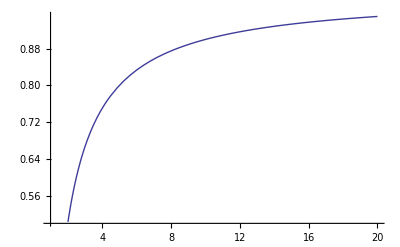

```mathematica
Plot[1-1/a,{a,1,20}]
```

## テスト1 指標1 (1D; M:2)

```mathematica
li[1,2]={{1},{2}}
```

{{1},{2}}

```mathematica
cl[1,2][1]={li[1,2]}
```

{{{1},{2}}}

```mathematica
cl[1,2][2]=Map[{#}&,li[1,2]]
```

{{{1}},{{2}}}

```mathematica
clusteringAdequationS[cl[1,2][1]]
```

2

```mathematica
clusteringAdequationS[cl[1,2][2]]
```

2

## テスト2 指標1 (1D; M:3)

```mathematica
li[1,3]={{1},{2},{3}}
```

{{1},{2},{3}}

```mathematica
cl[1,3][1]={li[1,3]}
```

{{{1},{2},{3}}}

```mathematica
cl[1,3][2]={{{1}},{{2},{3}}}
```

{{{1}},{{2},{3}}}

```mathematica
cl[1,3][3]=Map[{#}&,li[1,3]]
```

{{{1}},{{2}},{{3}}}

```mathematica
clusteringAdequationS[cl[1,3][1]]
```

3

```mathematica
clusteringAdequationS[cl[1,3][2]]//N
```

3.36359

```mathematica
clusteringAdequationS[cl[1,3][3]]
```

3

## テスト3 指標1,6 (1D; M:4)

```mathematica
li[1,4]=Table[{n},{n,4}]
```

{{1},{2},{3},{4}}

```mathematica
cl[1,4][1]={li[1,4]}
```

{{{1},{2},{3},{4}}}

```mathematica
cl[1,4][2]={{{1},{2}},{{3},{4}}}
```

{{{1},{2}},{{3},{4}}}

```mathematica
cl[1,4][2,2]={{{1}},{{2},{3},{4}}}
```

{{{1}},{{2},{3},{4}}}

```mathematica
cl[1,4][3]={{{1}},{{2},{3}},{{4}}}
```

{{{1}},{{2},{3}},{{4}}}

```mathematica
cl[1,4][3,2]={{{1}},{{2}},{{3},{4}}}
```

{{{1}},{{2}},{{3},{4}}}

```mathematica
cl[1,4][4]=Map[{#}&,li[1,4]]
```

{{{1}},{{2}},{{3}},{{4}}}

```mathematica
clusteringAdequationS[cl[1,4][1]]
```

4

```mathematica
clusteringAdequationS[cl[1,4][2]]//N
```

4.

```mathematica
clusteringAdequationS[cl[1,4][2,2]]//N
```

4.16017

```mathematica
clusteringAdequationS[cl[1,4][3]]//N
```

4.24264

```mathematica
clusteringAdequationS[cl[1,4][3,2]]//N
```

4.24264

```mathematica
clusteringAdequationS[cl[1,4][4]]//N
```

4.

```mathematica
clusteringAdequation6[cl[1,4][1]]
```

4

```mathematica
clusteringAdequation6[cl[1,4][2]]//N
```

4.

```mathematica
clusteringAdequation6[cl[1,4][2,2]]//N
```

4.16017

```mathematica
clusteringAdequation6[cl[1,4][3]]//N
```

4.24264

```mathematica
clusteringAdequation6[cl[1,4][3,2]]//N
```

3.75511

```mathematica
clusteringAdequation6[cl[1,4][4]]//N
```

4.

## テスト4 指標1 (1D; M:5)

### スケール:1

```mathematica
li[1,5]=Table[{n},{n,5}]
```

{{1},{2},{3},{4},{5}}

```mathematica
cl[1,5][1]={li[1,5]}
```

{{{1},{2},{3},{4},{5}}}

```mathematica
cl[1,5][2]={{{1},{2}},{{3},{4},{5}}}
```

{{{1},{2}},{{3},{4},{5}}}

```mathematica
cl[1,5][2,2]={{{1}},{{2},{3},{4},{5}}}
```

{{{1}},{{2},{3},{4},{5}}}

```mathematica
cl[1,5][3]={{{1}},{{2},{3},{4}},{{5}}}
```

{{{1}},{{2},{3},{4}},{{5}}}

```mathematica
cl[1,5][3,2]={{{1},{2}},{{3}},{{4},{5}}}
```

{{{1},{2}},{{3}},{{4},{5}}}

```mathematica
cl[1,5][3,3]={{{1}},{{2},{3}},{{4},{5}}}
```

{{{1}},{{2},{3}},{{4},{5}}}

```mathematica
cl[1,5][4]={{{1}},{{2}},{{3},{4}},{{5}}}
```

{{{1}},{{2}},{{3},{4}},{{5}}}

```mathematica
cl[1,5][4,2]={{{1}},{{2}},{{3}},{{4},{5}}}
```

{{{1}},{{2}},{{3}},{{4},{5}}}

```mathematica
cl[1,5][5]=Map[{#}&,li[1,5]]
```

{{{1}},{{2}},{{3}},{{4}},{{5}}}

```mathematica
clusteringAdequationS[cl[1,5][1]]
```

5

```mathematica
clusteringAdequationS[cl[1,5][2]]//N
```

4.91503

```mathematica
clusteringAdequationS[cl[1,5][2,2]]//N
```

6.3496

```mathematica
clusteringAdequationS[cl[1,5][3]]//N
```

5.52317

```mathematica
clusteringAdequationS[cl[1,5][3,2]]//N
```

5.34539

```mathematica
clusteringAdequationS[cl[1,5][3,3]]//N
```

5.34539

```mathematica
clusteringAdequationS[cl[1,5][4]]//N
```

5.33936

```mathematica
clusteringAdequationS[cl[1,5][4,2]]//N
```

5.33936

```mathematica
clusteringAdequationS[cl[1,5][5]]//N
```

5.

### スケール:2

```mathematica
li[1,5]=Table[{n},{n,5}]*2
```

{{2},{4},{6},{8},{10}}

```mathematica
cl[1,5][1]={li[1,5]}
```

{{{2},{4},{6},{8},{10}}}

```mathematica
cl[1,5][2]={{{2},{4}},{{6},{8},{10}}}
```

{{{2},{4}},{{6},{8},{10}}}

```mathematica
cl[1,5][2,2]={{{2}},{{4},{6},{8},{10}}}
```

{{{2}},{{4},{6},{8},{10}}}

```mathematica
cl[1,5][3]={{{2}},{{4},{6},{8}},{{10}}}
```

{{{2}},{{4},{6},{8}},{{10}}}

```mathematica
cl[1,5][3,2]={{{2},{4}},{{6}},{{8},{10}}}
```

{{{2},{4}},{{6}},{{8},{10}}}

```mathematica
cl[1,5][3,3]={{{2}},{{4},{6}},{{8},{10}}}
```

{{{2}},{{4},{6}},{{8},{10}}}

```mathematica
cl[1,5][4]={{{2}},{{4}},{{6},{8}},{{10}}}
```

{{{2}},{{4}},{{6},{8}},{{10}}}

```mathematica
cl[1,5][4,2]={{{2}},{{4}},{{6}},{{8},{10}}}
```

{{{2}},{{4}},{{6}},{{8},{10}}}

```mathematica
cl[1,5][5]=Map[{#}&,li[1,5]]
```

{{{2}},{{4}},{{6}},{{8}},{{10}}}

```mathematica
clusteringAdequationS[cl[1,5][1]]
```

5

```mathematica
clusteringAdequationS[cl[1,5][2]]//N
```

4.91503

```mathematica
clusteringAdequationS[cl[1,5][2,2]]//N
```

6.3496

```mathematica
clusteringAdequationS[cl[1,5][3]]//N
```

5.52317

```mathematica
clusteringAdequationS[cl[1,5][3,2]]//N
```

5.34539

```mathematica
clusteringAdequationS[cl[1,5][3,3]]//N
```

5.34539

```mathematica
clusteringAdequationS[cl[1,5][4]]//N
```

5.33936

```mathematica
clusteringAdequationS[cl[1,5][4,2]]//N
```

5.33936

```mathematica
clusteringAdequationS[cl[1,5][5]]//N
```

5.

## テスト5 指標1 (1D;M:8 * 4)

```mathematica
li[1,8,4]=Flatten[Table[{a,a},{a,8},{4}],1]
```

{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}

```mathematica
cl[1,8,4][32]=Map[{#}&,li[1,8,4]]
```

{{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{2,2}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{6,6}},{{6,6}},{{6,6}},{{6,6}},{{7,7}},{{7,7}},{{7,7}},{{7,7}},{{8,8}},{{8,8}},{{8,8}},{{8,8}}}

```mathematica
cl[1,8,4][16]=Partition[li[1,8,4],2]
```

{{{1,1},{1,1}},{{1,1},{1,1}},{{2,2},{2,2}},{{2,2},{2,2}},{{3,3},{3,3}},{{3,3},{3,3}},{{4,4},{4,4}},{{4,4},{4,4}},{{5,5},{5,5}},{{5,5},{5,5}},{{6,6},{6,6}},{{6,6},{6,6}},{{7,7},{7,7}},{{7,7},{7,7}},{{8,8},{8,8}},{{8,8},{8,8}}}

```mathematica
cl[1,8,4][8]=Split[li[1,8,4]]
```

{{{1,1},{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2},{2,2}},{{3,3},{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6},{6,6}},{{7,7},{7,7},{7,7},{7,7}},{{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][4]=FindClusters[li[1,8,4],4,Method->"Optimize"]
```

{{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
(*cl[1][4]={{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2}},{{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6}},{{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}*)
```

```mathematica
(*cl[1][4]={{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}},{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}},{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}},{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}}}*)
```

```mathematica
cl[1,8,4][2]={{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}
```

{{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][1]={{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}
```

{{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][1,"f"]=cl[1,8,4][1]
```

{{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][2,"f"]=cl[1,8,4][2]
```

{{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][4,"f"]=cl[1,8,4][4]
```

{{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][6,"f"]=FindClusters[li[1,8,4],6]
```

{{{1,1},{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2},{2,2}},{{3,3},{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6}},{{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][8,"f"]=cl[1,8,4][8]
```

{{{1,1},{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2},{2,2}},{{3,3},{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6},{6,6}},{{7,7},{7,7},{7,7},{7,7}},{{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][10,"f"]=FindClusters[li[1,8,4],10]
```

{{{1,1},{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2},{2,2}},{{3,3}},{{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6},{6,6}},{{7,7}},{{7,7},{7,7},{7,7}},{{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][12,"f"]=FindClusters[li[1,8,4],12]
```

{{{1,1}},{{1,1},{1,1},{1,1}},{{2,2}},{{2,2}},{{2,2},{2,2}},{{3,3},{3,3},{3,3},{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6}},{{6,6}},{{7,7},{7,7},{7,7},{7,7}},{{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][14,"f"]=FindClusters[li[1,8,4],14]
```

{{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{2,2},{2,2},{2,2}},{{2,2}},{{3,3},{3,3}},{{3,3}},{{3,3}},{{4,4},{4,4},{4,4},{4,4}},{{5,5},{5,5},{5,5},{5,5}},{{6,6},{6,6},{6,6},{6,6}},{{7,7},{7,7},{7,7},{7,7}},{{8,8},{8,8},{8,8},{8,8}}}

```mathematica
cl[1,8,4][16,"f"]=cl[1,8,4][16]
```

{{{1,1},{1,1}},{{1,1},{1,1}},{{2,2},{2,2}},{{2,2},{2,2}},{{3,3},{3,3}},{{3,3},{3,3}},{{4,4},{4,4}},{{4,4},{4,4}},{{5,5},{5,5}},{{5,5},{5,5}},{{6,6},{6,6}},{{6,6},{6,6}},{{7,7},{7,7}},{{7,7},{7,7}},{{8,8},{8,8}},{{8,8},{8,8}}}

```mathematica
Do[cl[1,8,4][n,"f"]=FindClusters[li[1,8,4],n,Method->"Optimize"],{n,3,7,2}]
```

```mathematica
Do[cl[1,8,4][n,"f"]=FindClusters[li[1,8,4],n,Method->"Agglomerate"],{n,9,15,2}]
```

```mathematica
Do[cl[1,8,4][n,"f"]=FindClusters[li[1,8,4],n],{n,17,31}]
```

```mathematica
cl[1,8,4][32,"f"]=cl[1,8,4][32]
```

{{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{2,2}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{6,6}},{{6,6}},{{6,6}},{{6,6}},{{7,7}},{{7,7}},{{7,7}},{{7,7}},{{8,8}},{{8,8}},{{8,8}},{{8,8}}}

指標1

```mathematica
scores[1,8,4]=Table[Log[clusteringAdequationS[cl[1,8,4][n,"f"]]],{n,1,32}]//N
```

{3.46574,3.46574,3.27508,3.0429,2.9576,2.83148,2.46577,2.07944,2.19722,2.30259,2.3979,2.48491,2.56495,2.63906,2.70805,2.77259,2.83321,2.89037,2.94444,2.99573,3.04452,3.09104,3.13549,3.17805,3.21888,3.2581,3.29584,3.3322,3.3673,3.4012,3.43399,3.46574}

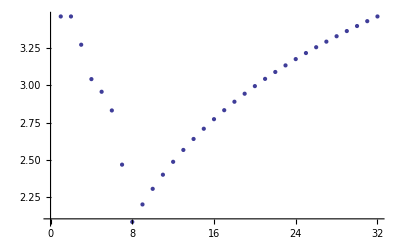

```mathematica
ListPlot[scores[1,8,4]]
```

指標2

```mathematica
scores2[1,8,4]=Table[clusteringAdequation2[cl[1,8,4][n,"f"]]//Log,{n,1,32}]//N
```

{9.80258,4.61418,3.22571,3.12766,2.87702,2.54175,2.33708,2.07944,2.19722,2.30259,2.3979,2.48491,2.56495,2.63906,2.70805,2.77259,2.83321,2.89037,2.94444,2.99573,3.04452,3.09104,3.13549,3.17805,3.21888,3.2581,3.29584,3.3322,3.3673,3.4012,3.43399,3.46574}

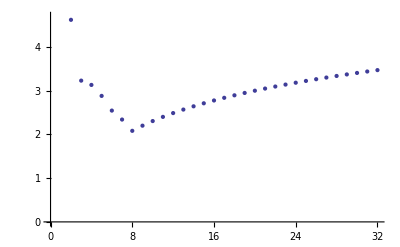

```mathematica
ListPlot[scores2[1,8,4]]
```

指標3

```mathematica
scores3[1,8,4]=Table[clusteringAdequationS2[cl[1,8,4][n,"f"]]//Log,{n,1,32}]//N
```

{3.46574,2.07944,1.83428,1.88386,1.94179,1.99655,2.03885,2.07944,2.19722,2.30259,2.3979,2.48491,2.56495,2.63906,2.70805,2.77259,2.83321,2.89037,2.94444,2.99573,3.04452,3.09104,3.13549,3.17805,3.21888,3.2581,3.29584,3.3322,3.3673,3.4012,3.43399,3.46574}

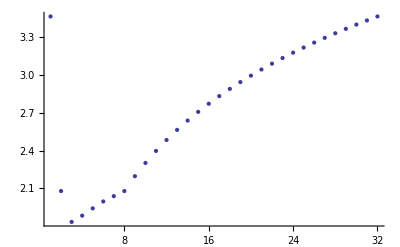

```mathematica
ListPlot[scores3[1,8,4],PlotRange->All]
```

指標4

```mathematica
scores4[1,8,4]=Table[clusteringAdequation4[cl[1,8,4][n,"f"],2]//Log,{n,1,32}]//N
```

{4.90129,2.65366,2.14463,2.13452,2.11775,2.10069,2.09012,2.07944,2.19722,2.30259,2.3979,2.48491,2.56495,2.63906,2.70805,2.77259,2.83321,2.89037,2.94444,2.99573,3.04452,3.09104,3.13549,3.17805,3.21888,3.2581,3.29584,3.3322,3.3673,3.4012,3.43399,3.46574}

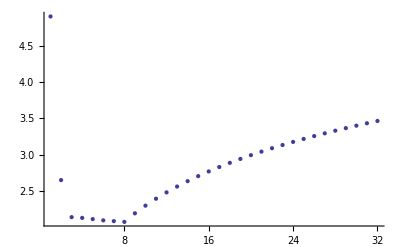

```mathematica
ListPlot[scores4[1,8,4],PlotRange->All]
```

```mathematica
scores5[1,8,4]=Table[clusteringAdequation5[cl[1,8,4][n,"f"],2]//Log,{n,1,32}]//N
```

{1.73287,1.38629,1.46395,1.61466,1.75957,1.88611,1.98744,2.07944,2.19722,2.30259,2.3979,2.48491,2.56495,2.63906,2.70805,2.77259,2.83321,2.89037,2.94444,2.99573,3.04452,3.09104,3.13549,3.17805,3.21888,3.2581,3.29584,3.3322,3.3673,3.4012,3.43399,3.46574}

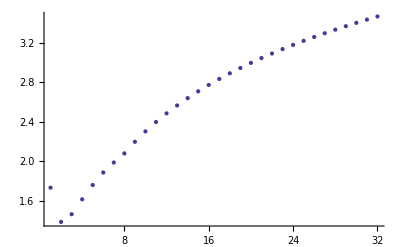

```mathematica
ListPlot[scores5[1,8,4],PlotRange->All]
```

## テスト6 指標1,2 (ランダムデータ)

```mathematica
rt2=Table[{RandomReal[{1,30}],RandomReal[{1,30}]},{8}]
```

{{17.2334,27.4091},{22.1542,23.5509},{23.5897,6.4204},{16.4595,23.3693},{28.7135,12.0748},{20.8557,15.5144},{18.8848,18.4494},{22.5902,11.5148}}

```mathematica
rt2={{25.15634067913374,17.778315333739826},{5.393424519638437,11.843838530874969},{11.681842938244394,21.294400340505824},{26.676786513760746,19.13656591747774},{15.795868678026508,15.078525778980726},{17.29924180699281,15.291122911688632},{27.10723338749886,9.453545934292713},{11.97369213035551,6.0326199477234965}}
```

{{25.1563,17.7783},{5.39342,11.8438},{11.6818,21.2944},{26.6768,19.1366},{15.7959,15.0785},{17.2992,15.2911},{27.1072,9.45355},{11.9737,6.03262}}

```mathematica
cl[2][1]={rt2}
```

{{{25.1563,17.7783},{5.39342,11.8438},{11.6818,21.2944},{26.6768,19.1366},{15.7959,15.0785},{17.2992,15.2911},{27.1072,9.45355},{11.9737,6.03262}}}

```mathematica
cl[2][8]=Map[{#}&,rt2]
```

{{{25.1563,17.7783}},{{5.39342,11.8438}},{{11.6818,21.2944}},{{26.6768,19.1366}},{{15.7959,15.0785}},{{17.2992,15.2911}},{{27.1072,9.45355}},{{11.9737,6.03262}}}

```mathematica
Do[cl[2][n]=FindClusters[rt2,n,Method->"Agglomerate"],{n,2,7,1}]
```

```mathematica
Do[cl[2][n]=FindClusters[rt2,n,Method->"Optimize"],{n,2,7,1}]
```

```mathematica
cl[2][3]
```

{{{25.1563,17.7783},{26.6768,19.1366},{27.1072,9.45355}},{{5.39342,11.8438},{11.9737,6.03262}},{{11.6818,21.2944},{15.7959,15.0785},{17.2992,15.2911}}}

```mathematica
Graphics[Map[Point[#]&,rt2]]
```

-Graphics-

```mathematica
rt2//Sort
```

{{5.39342,11.8438},{11.6818,21.2944},{11.9737,6.03262},{15.7959,15.0785},{17.2992,15.2911},{25.1563,17.7783},{26.6768,19.1366},{27.1072,9.45355}}

```mathematica
cl[2][3]={{{5.393424519638437,11.843838530874969},{11.681842938244394,21.294400340505824},{11.97369213035551,6.0326199477234965},{15.795868678026508,15.078525778980726},{17.29924180699281,15.291122911688632}},{{25.15634067913374,17.778315333739826},{26.676786513760746,19.13656591747774}},{{27.10723338749886,9.453545934292713}}}
```

{{{5.39342,11.8438},{11.6818,21.2944},{11.9737,6.03262},{15.7959,15.0785},{17.2992,15.2911}},{{25.1563,17.7783},{26.6768,19.1366}},{{27.1072,9.45355}}}

```mathematica
clusteringAdequation[cl[2][3]]//Log
```

19.5132

```mathematica
scores[2]=Table[Log[clusteringAdequation[cl[2][n]]],{n,1,8}]
```

{16.5438,20.1025,19.5132,18.6524,17.3852,15.4878,16.0077,16.5438}

```mathematica
scoresS[2]=Table[Log[clusteringAdequationS[cl[2][n]]],{n,1,8}]
```

{2.07944,2.52675,2.45267,2.34448,2.1852,1.94671,2.01205,2.07944}

```mathematica
scores2[2]=Table[Log[clusteringAdequation2[cl[2][n]]],{n,1,8}]
```

{16.5438,10.07,10.0663,4.2784,3.97343,2.04376,2.04025,2.07944}

```mathematica
scores3[2]=Table[Log[clusteringAdequation3[cl[2][n],2]],{n,1,8}]
```

{Log[clusteringAdequation3[{{{25.1563,17.7783},{5.39342,11.8438},{11.6818,21.2944},{26.6768,19.1366},{15.7959,15.0785},{17.2992,15.2911},{27.1072,9.45355},{11.9737,6.03262}}},2]],Log[clusteringAdequation3[{{{25.1563,17.7783},{26.6768,19.1366},{27.1072,9.45355}},{{5.39342,11.8438},{11.6818,21.2944},{15.7959,15.0785},{17.2992,15.2911},{11.9737,6.03262}}},2]],Log[clusteringAdequation3[{{{5.39342,11.8438},{11.6818,21.2944},{11.9737,6.03262},{15.7959,15.0785},{17.2992,15.2911}},{{25.1563,17.7783},{26.6768,19.1366}},{{27.1072,9.45355}}},2]],Log[clusteringAdequation3[{{{25.1563,17.7783},{26.6768,19.1366}},{{5.39342,11.8438},{11.9737,6.03262}},{{11.6818,21.2944},{15.7959,15.0785},{17.2992,15.2911}},{{27.1072,9.45355}}},2]],Log[clusteringAdequation3[{{{25.1563,17.7783},{26.6768,19.1366}},{{5.39342,11.8438}},{{11.6818,21.2944},{15.7959,15.0785},{17.2992,15.2911}},{{27.1072,9.45355}},{{11.9737,6.03262}}},2]],Log[clusteringAdequation3[{{{25.1563,17.7783},{26.6768,19.1366}},{{5.39342,11.8438}},{{11.6818,21.2944}},{{15.7959,15.0785},{17.2992,15.2911}},{{27.1072,9.45355}},{{11.9737,6.03262}}},2]],Log[clusteringAdequation3[{{{25.1563,17.7783}},{{5.39342,11.8438}},{{11.6818,21.2944}},{{26.6768,19.1366}},{{15.7959,15.0785},{17.2992,15.2911}},{{27.1072,9.45355}},{{11.9737,6.03262}}},2]],Log[clusteringAdequation3[{{{25.1563,17.7783}},{{5.39342,11.8438}},{{11.6818,21.2944}},{{26.6768,19.1366}},{{15.7959,15.0785}},{{17.2992,15.2911}},{{27.1072,9.45355}},{{11.9737,6.03262}}},2]]}

```mathematica
clusteringAdequation[cl[2][1]]//Log
```

16.5438

```mathematica
clusteringAdequation[cl[2][8]]//Log
```

16.5438

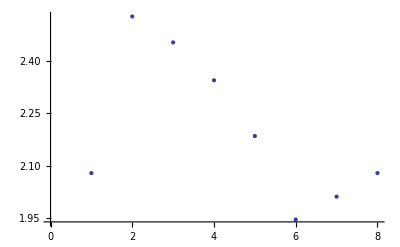

```mathematica
ListPlot[scoresS[2]]
```

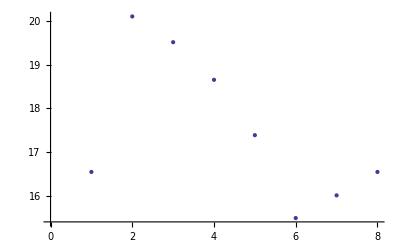

```mathematica
ListPlot[scores[2]]
```

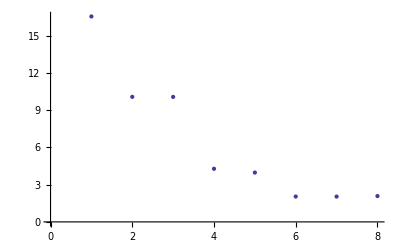

```mathematica
ListPlot[scores2[2]]
```

```mathematica
ListPlot[scores3[2]]
```

-Graphics-

## テスト7 指標1 (ランダムデータ(テスト2のデータ);全探索)

全クラスタリングパターン: combination.nb8.nb

### 2 clusters

```mathematica
rt2={{25.15634067913374,17.778315333739826},{5.393424519638437,11.843838530874969},{11.681842938244394,21.294400340505824},{26.676786513760746,19.13656591747774},{15.795868678026508,15.078525778980726},{17.29924180699281,15.291122911688632},{27.10723338749886,9.453545934292713},{11.97369213035551,6.0326199477234965}}
```

{{25.1563,17.7783},{5.39342,11.8438},{11.6818,21.2944},{26.6768,19.1366},{15.7959,15.0785},{17.2992,15.2911},{27.1072,9.45355},{11.9737,6.03262}}

```mathematica
Graphics[Map[Point[#]&,rt2]]
```

-Graphics-

```mathematica
score["rt2"][7,1]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[7,1][[n]]]]//Log,{n,Length[sets[7,1]]}];
```

```mathematica
score["rt2"][6,2]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[6,2][[n]]]]//Log,{n,Length[sets[6,2]]}];
```

```mathematica
score["rt2"][5,3]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[5,3][[n]]]]//Log,{n,Length[sets[5,3]]}];
```

```mathematica
score["rt2"][4,4]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[4,4][[n]]]]//Log,{n,Length[sets[4,4]]}];
```

```mathematica
{score["rt2"][7,1],score["rt2"][6,2],score["rt2"][5,3],score["rt2"][4,4]}//Min
```

-∞

```mathematica
Position[{score["rt2"][7,1],score["rt2"][6,2],score["rt2"][5,3],score["rt2"][4,4]},{score["rt2"][7,1],score["rt2"][6,2],score["rt2"][5,3],score["rt2"][4,4]}//Min]
```

{{1,1},{1,2},{2,1},{2,2},{3,1},{3,2},{4,1},{4,2}}

### 3 clusters

```mathematica
rt2={{25.15634067913374,17.778315333739826},{5.393424519638437,11.843838530874969},{11.681842938244394,21.294400340505824},{26.676786513760746,19.13656591747774},{15.795868678026508,15.078525778980726},{17.29924180699281,15.291122911688632},{27.10723338749886,9.453545934292713},{11.97369213035551,6.0326199477234965}}
```

{{25.1563,17.7783},{5.39342,11.8438},{11.6818,21.2944},{26.6768,19.1366},{15.7959,15.0785},{17.2992,15.2911},{27.1072,9.45355},{11.9737,6.03262}}

```mathematica
Graphics[Map[Point[#]&,rt2]]
```

-Graphics-

```mathematica
score["rt2"][6,1,1]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[6,1,1][[n]]]]//Log,{n,Length[sets[6,1,1]]}];
```

```mathematica
score["rt2"][5,2,1]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[5,2,1][[n]]]]//Log,{n,Length[sets[5,2,1]]}];
```

```mathematica
score["rt2"][4,3,1]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[4,3,1][[n]]]]//Log,{n,Length[sets[4,3,1]]}];
```

```mathematica
score["rt2"][4,2,2]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[4,2,2][[n]]]]//Log,{n,Length[sets[4,2,2]]}];
```

```mathematica
score["rt2"][3,3,2]=Table[clusteringAdequationS[Map[rt2[[#]]&,sets[3,3,2][[n]]]]//Log,{n,Length[sets[3,3,2]]}];
```

```mathematica
{score["rt2"][6,1,1],score["rt2"][5,2,1],score["rt2"][4,3,1],score["rt2"][4,2,2],score["rt2"][3,3,2]}//Min
```

2.45267

```mathematica
Exp[2.45266919713492]
```

11.6193

## 計算めも

```mathematica
tmpcl=FindClusters[rt2,2,Method->"Agglomerate"]
```

{{{25.1563,17.7783},{11.6818,21.2944},{26.6768,19.1366},{15.7959,15.0785},{17.2992,15.2911},{27.1072,9.45355}},{{5.39342,11.8438},{11.9737,6.03262}}}

```mathematica
tmpcl=FindClusters[rt2,2,Method->"Optimize"]
```

{{{25.1563,17.7783},{26.6768,19.1366},{27.1072,9.45355}},{{5.39342,11.8438},{11.6818,21.2944},{15.7959,15.0785},{17.2992,15.2911},{11.9737,6.03262}}}

```mathematica
clusteringAdequation[tmpcl]//Log
```

20.1025

```mathematica
clusteringAdequation[{{{1,1}},{{2,2},{3,4}}}]
```

2^((√5)/2+1/3 (2+(√34)/3))

```mathematica
clusteringAdequation[{{{1}},{{2}},{{3}}}]
```

3^(2/3)

```mathematica
clusteringAdequation[{{{1},{2},{3}}}]
```

3^(2/3)

## テスト8 指標1 (1D,M:3-5)

### M:3

```mathematica
li[4]={{1,1},{2,2},{3,3}}
```

{{1,1},{2,2},{3,3}}

```mathematica
cl[4][1]={li[4]}
```

{{{1,1},{2,2},{3,3}}}

```mathematica
cl[4][3]=Map[{#}&,li[4]]
```

{{{1,1}},{{2,2}},{{3,3}}}

```mathematica
cl[4][2]={{{1,1},{2,2}},{{3,3}}}
```

{{{1,1},{2,2}},{{3,3}}}

```mathematica
cl[4][2,2]={{{1,1},{3,3}},{{2,2}}}
```

{{{1,1},{3,3}},{{2,2}}}

```mathematica
clusteringAdequationS[cl[4][1]]//Log//N
```

1.09861

```mathematica
clusteringAdequationS[cl[4][2]]//Log//N
```

1.21301

```mathematica
clusteringAdequationS[cl[4][2,2]]//Log//N
```

1.73287

```mathematica
clusteringAdequationS[cl[4][3]]//Log//N
```

1.09861

### M:4

```mathematica
li[5]={{1,1},{2,2},{3,3},{4,4}}
```

{{1,1},{2,2},{3,3},{4,4}}

```mathematica
cl[5][1]={li[5]}
```

{{{1,1},{2,2},{3,3},{4,4}}}

```mathematica
cl[5][4]=Map[{#}&,li[5]]
```

{{{1,1}},{{2,2}},{{3,3}},{{4,4}}}

```mathematica
cl[5][2]={{{1,1},{2,2}},{{3,3},{4,4}}}
```

{{{1,1},{2,2}},{{3,3},{4,4}}}

```mathematica
cl[5][3]={{{1,1}},{{2,2},{3,3}},{{4,4}}}
```

{{{1,1}},{{2,2},{3,3}},{{4,4}}}

```mathematica
cl[5][3,2]={{{1,1}},{{2,2}},{{3,3},{4,4}}}
```

{{{1,1}},{{2,2}},{{3,3},{4,4}}}

```mathematica
cl[5][3,3]={{{3,3}},{{2,2}},{{1,1},{4,4}}}
```

{{{3,3}},{{2,2}},{{1,1},{4,4}}}

```mathematica
clusteringAdequationS[cl[5][1]]//Log//N
```

1.38629

```mathematica
clusteringAdequationS[cl[5][2]]//Log//N
```

1.38629

```mathematica
clusteringAdequationS[cl[5][3]]//Log//N
```

1.44519

```mathematica
clusteringAdequationS[cl[5][3,2]]//Log//N
```

1.44519

```mathematica
clusteringAdequationS[cl[5][3,3]]//Log//N
```

2.13833

```mathematica
clusteringAdequationS[cl[5][4]]//Log//N
```

1.38629

### M:5

```mathematica
li[6]={{1,1},{2,2},{3,3},{4,4},{5,5}}
```

{{1,1},{2,2},{3,3},{4,4},{5,5}}

```mathematica
cl[6][1]={li[6]}
```

{{{1,1},{2,2},{3,3},{4,4},{5,5}}}

```mathematica
cl[6][5]=Map[{#}&,li[6]]
```

{{{1,1}},{{2,2}},{{3,3}},{{4,4}},{{5,5}}}

```mathematica
cl[6][2]={{{1,1},{2,2}},{{3,3},{4,4},{5,5}}}
```

{{{1,1},{2,2}},{{3,3},{4,4},{5,5}}}

```mathematica
cl[6][3]={{{1,1},{2,2}},{{3,3}},{{4,4},{5,5}}}
```

{{{1,1},{2,2}},{{3,3}},{{4,4},{5,5}}}

```mathematica
cl[6][3,2]={{{1,1}},{{2,2},{3,3},{4,4}},{{5,5}}}
```

{{{1,1}},{{2,2},{3,3},{4,4}},{{5,5}}}

```mathematica
cl[6][3,3]={{{1,1},{2,2},{3,3}},{{4,4}},{{5,5}}}
```

{{{1,1},{2,2},{3,3}},{{4,4}},{{5,5}}}

```mathematica
cl[6][3,4]={{{1,1},{5,5}},{{2,2}},{{3,3}},{{4,4}}}
```

{{{1,1},{5,5}},{{2,2}},{{3,3}},{{4,4}}}

```mathematica
cl[6][3,5]={{{1,1}},{{2,2}},{{3,3},{4,4}},{{5,5}}}
```

{{{1,1}},{{2,2}},{{3,3},{4,4}},{{5,5}}}

```mathematica
cl[6][3,6]={{{1,1}},{{2,2},{3,3}},{{4,4}},{{5,5}}}
```

{{{1,1}},{{2,2},{3,3}},{{4,4}},{{5,5}}}

```mathematica
cl[6][4]={{{1,1},{2,2}},{{3,3}},{{4,4}},{{5,5}}}
```

{{{1,1},{2,2}},{{3,3}},{{4,4}},{{5,5}}}

```mathematica
cl[6][4]={{{1,1}},{{2,2},{3,3}},{{4,4}},{{5,5}}}
```

{{{1,1}},{{2,2},{3,3}},{{4,4}},{{5,5}}}

```mathematica
clusteringAdequationS[cl[6][1]]//Log//N
```

1.60944

```mathematica
clusteringAdequationS[cl[6][2]]//Log//N
```

1.5923

```mathematica
clusteringAdequationS[cl[6][3]]//Log//N
```

1.67623

```mathematica
clusteringAdequationS[cl[6][3,2]]//Log//N
```

1.70895

```mathematica
clusteringAdequationS[cl[6][3,3]]//Log//N
```

1.70895

```mathematica
clusteringAdequationS[cl[6][3,4]]//Log//N
```

2.54154

```mathematica
clusteringAdequationS[cl[6][3,5]]//Log//N
```

1.67511

```mathematica
clusteringAdequationS[cl[6][3,6]]//Log//N
```

1.67511

```mathematica
clusteringAdequationS[cl[6][4]]//Log//N
```

1.67511

```mathematica
clusteringAdequationS[cl[6][5]]//Log//N
```

1.60944

## テスト9 指標1 (3D,M:3)

```mathematica
li[5]={{0,0,1},{0,1,0},{1,0,0}}
```

{{0,0,1},{0,1,0},{1,0,0}}

```mathematica
cl[5][1]={li[5]}
```

{{{0,0,1},{0,1,0},{1,0,0}}}

```mathematica
cl[5][2]={{{0,0,1}},{{0,1,0},{1,0,0}}}
```

{{{0,0,1}},{{0,1,0},{1,0,0}}}

```mathematica
cl[5][3]=Map[{#}&,li[5]]
```

{{{0,0,1}},{{0,1,0}},{{1,0,0}}}

```mathematica
clusteringAdequation[cl[5][1]]//Log//N
```

0.897013

```mathematica
clusteringAdequation[cl[5][2]]//Log//N
```

1.05608

```mathematica
clusteringAdequation[cl[5][3]]//Log//N
```

0.897013

## テスト10 指標1 (2D,M:6,circle)

### r=1

```mathematica
Table[2 Pi n/6,{n,1,6}]
```

{π/3,(2 π)/3,π,(4 π)/3,(5 π)/3,2 π}

```mathematica
rt6=Map[polarToxy[{1,#}]&,Table[2 Pi n/6,{n,1,6}]]
```

{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt6]]
```

-Graphics-

```mathematica
cl[6][1]={rt6}
```

{{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}}

```mathematica
cl[6][1,5]={rt6[[{1}]],rt6[[2;;6]]}
```

{{{1/2,(√3)/2}},{{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}}

```mathematica
cl[6][2,4]={rt6[[1;;2]],rt6[[3;;6]]}
```

{{{1/2,(√3)/2},{-1/2,(√3)/2}},{{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}}

```mathematica
cl[6][2,4,2]={rt6[[{1,4}]],rt6[[{2,3,5,6}]]}
```

{{{1/2,(√3)/2},{-1/2,-(√3)/2}},{{-1/2,(√3)/2},{-1,0},{1/2,-(√3)/2},{1,0}}}

```mathematica
cl[6][3,3]={rt6[[1;;3]],rt6[[5;;6]]}
```

{{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0}},{{1/2,-(√3)/2},{1,0}}}

```mathematica
cl[6][6]=Map[{#}&,rt6]
```

{{{1/2,(√3)/2}},{{-1/2,(√3)/2}},{{-1,0}},{{-1/2,-(√3)/2}},{{1/2,-(√3)/2}},{{1,0}}}

```mathematica
clusteringAdequation[cl[6][1]]//Log//N
```

1.79176

```mathematica
clusteringAdequationS[cl[6][1]]//Log//N
```

1.79176

```mathematica
clusteringAdequationS[cl[6][1,5]]//Log//N
```

2.25756

```mathematica
clusteringAdequationS[cl[6][2,4]]//Log//N
```

2.25353

```mathematica
clusteringAdequationS[cl[6][2,4,2]]//Log//N
```

2.77259

```mathematica
clusteringAdequationS[cl[6][3,3]]//Log//N
```

1.83979

```mathematica
clusteringAdequationS[cl[6][6]]//Log//N
```

1.79176

### r=2

```mathematica
Table[2 Pi n/6,{n,1,6}]
```

{π/3,(2 π)/3,π,(4 π)/3,(5 π)/3,2 π}

```mathematica
rt6=Map[polarToxy[{2,#}]&,Table[2 Pi n/6,{n,1,6}]]
```

{{1,√3},{-1,√3},{-2,0},{-1,-√3},{1,-√3},{2,0}}

```mathematica
Graphics[Map[Point[#]&,rt6]]
```

-Graphics-

```mathematica
cl[6][1]={rt6}
```

{{{1,√3},{-1,√3},{-2,0},{-1,-√3},{1,-√3},{2,0}}}

```mathematica
cl[6][1,5]={rt6[[{1}]],rt6[[2;;6]]}
```

{{{1,√3}},{{-1,√3},{-2,0},{-1,-√3},{1,-√3},{2,0}}}

```mathematica
cl[6][2,4]={rt6[[1;;2]],rt6[[3;;6]]}
```

{{{1,√3},{-1,√3}},{{-2,0},{-1,-√3},{1,-√3},{2,0}}}

```mathematica
cl[6][2,4,2]={rt6[[{1,4}]],rt6[[{2,3,5,6}]]}
```

{{{1,√3},{-1,-√3}},{{-1,√3},{-2,0},{1,-√3},{2,0}}}

```mathematica
cl[6][3,3]={rt6[[1;;3]],rt6[[5;;6]]}
```

{{{1,√3},{-1,√3},{-2,0}},{{1,-√3},{2,0}}}

```mathematica
cl[6][6]=Map[{#}&,rt6]
```

{{{1,√3}},{{-1,√3}},{{-2,0}},{{-1,-√3}},{{1,-√3}},{{2,0}}}

```mathematica
clusteringAdequation[cl[6][1]]//Log//N
```

3.58352

```mathematica
clusteringAdequationS[cl[6][1]]//Log//N
```

1.79176

```mathematica
clusteringAdequationS[cl[6][1,5]]//Log//N
```

2.25756

```mathematica
clusteringAdequationS[cl[6][2,4]]//Log//N
```

2.25353

```mathematica
clusteringAdequationS[cl[6][2,4,2]]//Log//N
```

2.77259

```mathematica
clusteringAdequationS[cl[6][3,3]]//Log//N
```

1.83979

```mathematica
clusteringAdequationS[cl[6][6]]//Log//N
```

1.79176

## テスト11 指標1 (2D,M:7,circle)

### r=1

```mathematica
rt7=Map[polarToxy[{1,#}]&,Table[2 Pi n/7,{n,1,7}]]
```

{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt7]]
```

-Graphics-

```mathematica
cl[7][1]={rt7}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}}

```mathematica
cl[7][1,6]={rt7[[{1}]],rt7[[2;;7]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]}},{{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}}

```mathematica
cl[7][2,5]={rt7[[1;;2]],rt7[[3;;7]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]}},{{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}}

```mathematica
cl[7][3,4]={rt7[[1;;3]],rt7[[5;;7]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]}},{{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}}

```mathematica
cl[7][3,3,1]={rt7[[1;;3]],rt7[[5;;6]],rt7[[{7}]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]}},{{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]}},{{1,0}}}

```mathematica
cl[7][2,2,3]={rt7[[1;;2]],rt7[[3;;4]],rt7[[5;;7]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]}},{{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]}},{{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}}

```mathematica
cl[7][1,1,5]={rt7[[{1}]],rt7[[{2}]],rt7[[3;;7]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]}},{{-Sin[π/14],Cos[π/14]}},{{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]},{1,0}}}

```mathematica
cl[7][3,2,1,1]={rt7[[{1,2,3}]],rt7[[{4,5}]],rt7[[{6}]],rt7[[{7}]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]}},{{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]}},{{Sin[(3 π)/14],-Cos[(3 π)/14]}},{{1,0}}}

```mathematica
cl[7][2,2,2,1]={rt7[[{1,2}]],rt7[[{3,4}]],rt7[[{5,6}]],rt7[[{7}]]}
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]}},{{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]}},{{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]}},{{1,0}}}

```mathematica
cl[7][7]=Map[{#}&,rt7]
```

{{{Sin[(3 π)/14],Cos[(3 π)/14]}},{{-Sin[π/14],Cos[π/14]}},{{-Cos[π/7],Sin[π/7]}},{{-Cos[π/7],-Sin[π/7]}},{{-Sin[π/14],-Cos[π/14]}},{{Sin[(3 π)/14],-Cos[(3 π)/14]}},{{1,0}}}

指標1

```mathematica
clusteringAdequationS[cl[7][1]]//Log//N
```

1.94591

```mathematica
clusteringAdequationS[cl[7][1,6]]//Log//N
```

2.44968

```mathematica
clusteringAdequationS[cl[7][2,5]]//Log//N
```

2.4621

```mathematica
clusteringAdequationS[cl[7][3,4]]//Log//N
```

2.06384

```mathematica
clusteringAdequationS[cl[7][3,3,1]]//Log//N
```

2.09073

```mathematica
clusteringAdequationS[cl[7][2,2,3]]//Log//N
```

2.37197

```mathematica
clusteringAdequationS[cl[7][1,1,5]]//Log//N
```

2.56682

```mathematica
clusteringAdequationS[cl[7][3,2,1,1]]//Log//N
```

2.35891

```mathematica
clusteringAdequationS[cl[7][2,2,2,1]]//Log//N
```

2.28853

```mathematica
clusteringAdequationS[cl[7][7]]//Log//N
```

1.94591

指標6

```mathematica
clusteringAdequation6[cl[7][1]]//Log//N
```

N::meprec: 1/7\ (-1 + 2\ Cos[π/7] + 2\ Sin[π/14] - 2\ Sin[3\ π/14]) + 1/7\ (1 - 2\ Cos[π/7] - 2\ Sin[π/14] + 2\ Sin[3\ π/14])の評価中に内部精度限界$MaxExtraPrecision = 50.に達しました．

N::meprec: Log[Abs[1/7\ (-1 + 2\ Cos[Times[« 2 »]] + 2\ Sin[Times[« 2 »]] - 2\ Sin[Times[« 2 »]]) + 1/7\ (1 - 2\ Cos[Times[« 2 »]] - 2\ Sin[Times[« 2 »]] + 2\ Sin[Times[« 2 »]])]]の評価中に内部精度限界$MaxExtraPrecision = 50.に達しました．

1.94591

```mathematica
clusteringAdequation6[cl[7][1,6]]//Log//N
```

2.16087

```mathematica
clusteringAdequation6[cl[7][2,5]]//Log//N
```

2.2061

```mathematica
clusteringAdequation6[cl[7][3,4]]//Log//N
```

1.88699

```mathematica
clusteringAdequation6[cl[7][3,3,1]]//Log//N
```

1.90021

```mathematica
clusteringAdequation6[cl[7][2,2,3]]//Log//N
```

2.20045

```mathematica
clusteringAdequation6[cl[7][1,1,5]]//Log//N
```

2.21866

```mathematica
clusteringAdequation6[cl[7][3,2,1,1]]//Log//N
```

2.16903

```mathematica
clusteringAdequation6[cl[7][2,2,2,1]]//Log//N
```

N::meprec: 1/2\ (-Cos[π/14] - Cos[3\ π/14]) + 1/2\ (Cos[π/14] + Cos[3\ π/14])の評価中に内部精度限界$MaxExtraPrecision = 50.に達しました．

General::stop: この計算中に，N :: meprecのこれ以上の出力は表示されません．

2.17215

```mathematica
clusteringAdequation6[cl[7][7]]//Log//N
```

1.94591

## テスト12 指標1 (2D,M:8,circle,全探索)

全クラスタリングパターン: combination.nb8.nb

```mathematica
rt8=Map[polarToxy[{1,#}]&,Table[2 Pi n/8,{n,1,8}]]
```

{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)},{0,-1},{1/(√2),-1/(√2)},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt8]]
```

-Graphics-

### 1 cluster

```mathematica
clusteringAdequationS[{rt8}]
```

8

```mathematica
1-1/(8)
```

7/8

```mathematica
clusteringAdequationS[{rt8}]//Log//N
```

2.07944

```mathematica
clusteringAdequationS2[{rt8}]//Log//N
```

2.07944

```mathematica
clusteringAdequationS2[{rt8}*10]//Log//N
```

2.07944

### 2 clusters

```mathematica
IntegerPartitions[8,{2}]
```

{{7,1},{6,2},{5,3},{4,4}}

```mathematica
cl[8][2]={rt8[[1;;4]],rt8[[5;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)},{0,-1},{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][5,3]={rt8[[1;;5]],rt8[[6;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)}},{{0,-1},{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][6,2]={rt8[[1;;6]],rt8[[7;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][7,1]={rt8[[1;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)},{0,-1},{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][7,1]*6
```

{{{3 √2,3 √2},{0,6},{-3 √2,3 √2},{-6,0},{-3 √2,-3 √2},{0,-6},{3 √2,-3 √2}},{{6,0}}}

指標1

```mathematica
clusteringAdequationS[cl[8][2]]//Log//N
```

2.67746

```mathematica
clusteringAdequationS[cl[8][5,3]]//Log//N
```

2.64638

```mathematica
clusteringAdequationS[cl[8][6,2]]//Log//N
```

2.634

```mathematica
clusteringAdequationS[cl[8][7,1]]//Log//N
```

2.61071

```mathematica
clusteringAdequationS[cl[8][7,1]*6]//Log//N
```

2.61071

指標3

```mathematica
clusteringAdequationS2[cl[8][2]]//Log//N
```

1.68531

```mathematica
clusteringAdequationS2[cl[8][5,3]]//Log//N
```

1.74113

```mathematica
clusteringAdequationS2[cl[8][6,2]]//Log//N
```

1.89398

```mathematica
clusteringAdequationS2[cl[8][7,1]]//Log//N
```

2.05468

```mathematica
clusteringAdequationS2[cl[8][7,1]*6]//Log//N
```

2.05468

### 3 clusters (全探索)

指標1

```mathematica
score[8][6,1,1]=Table[clusteringAdequationS[Map[rt8[[#]]&,sets[6,1,1][[n]]]]//Log//N,{n,Length[sets[6,1,1]]}];
```

```mathematica
score[8][5,2,1]=Table[clusteringAdequationS[Map[rt8[[#]]&,sets[5,2,1][[n]]]]//Log//N,{n,Length[sets[5,2,1]]}];
```

```mathematica
score[8][4,3,1]=Table[clusteringAdequationS[Map[rt8[[#]]&,sets[4,3,1][[n]]]]//Log//N,{n,Length[sets[4,3,1]]}];
```

```mathematica
score[8][4,2,2]=Table[clusteringAdequationS[Map[rt8[[#]]&,sets[4,2,2][[n]]]]//Log//N,{n,Length[sets[4,2,2]]}];
```

```mathematica
score[8][3,3,2]=Table[clusteringAdequationS[Map[rt8[[#]]&,sets[3,3,2][[n]]]]//Log//N,{n,Length[sets[3,3,2]]}];
```

```mathematica
Min[{score[8][6,1,1],score[8][5,2,1],score[8][4,3,1],score[8][4,2,2],score[8][3,3,2]}]
```

2.55249

```mathematica
Position[{score[8][6,1,1],score[8][5,2,1],score[8][4,3,1],score[8][4,2,2],score[8][3,3,2]},Min[{score[8][6,1,1],score[8][5,2,1],score[8][4,3,1],score[8][4,2,2],score[8][3,3,2]}]]
```

{{5,1},{5,10},{5,51},{5,60},{5,201},{5,210},{5,216},{5,217},{5,363},{5,370},{5,461},{5,466},{5,523},{5,527},{5,551},{5,560}}

指標3

```mathematica
score3[8][6,1,1]=Table[clusteringAdequationS2[Map[rt8[[#]]&,sets[6,1,1][[n]]]]//Log//N,{n,Length[sets[6,1,1]]}];
```

```mathematica
score3[8][5,2,1]=Table[clusteringAdequationS2[Map[rt8[[#]]&,sets[5,2,1][[n]]]]//Log//N,{n,Length[sets[5,2,1]]}];
```

```mathematica
score3[8][4,3,1]=Table[clusteringAdequationS2[Map[rt8[[#]]&,sets[4,3,1][[n]]]]//Log//N,{n,Length[sets[4,3,1]]}];
```

```mathematica
score3[8][4,2,2]=Table[clusteringAdequationS2[Map[rt8[[#]]&,sets[4,2,2][[n]]]]//Log//N,{n,Length[sets[4,2,2]]}];
```

```mathematica
score3[8][3,3,2]=Table[clusteringAdequationS2[Map[rt8[[#]]&,sets[3,3,2][[n]]]]//Log//N,{n,Length[sets[3,3,2]]}];
```

```mathematica
Min[{score3[8][6,1,1],score3[8][5,2,1],score3[8][4,3,1],score3[8][4,2,2],score3[8][3,3,2]}]
```

1.5948

```mathematica
Position[{score3[8][6,1,1],score3[8][5,2,1],score3[8][4,3,1],score3[8][4,2,2],score3[8][3,3,2]},Min[{score3[8][6,1,1],score3[8][5,2,1],score3[8][4,3,1],score3[8][4,2,2],score3[8][3,3,2]}]]
```

{{5,1},{5,10},{5,51},{5,60},{5,201},{5,210},{5,216},{5,217},{5,363},{5,370},{5,461},{5,466},{5,523},{5,527},{5,551},{5,560}}

```mathematica
Max[{score3[8][6,1,1],score3[8][5,2,1],score3[8][4,3,1],score3[8][4,2,2],score3[8][3,3,2]}]
```

2.07944

```mathematica
Position[{score3[8][6,1,1],score3[8][5,2,1],score3[8][4,3,1],score3[8][4,2,2],score3[8][3,3,2]},Max[{score3[8][6,1,1],score3[8][5,2,1],score3[8][4,3,1],score3[8][4,2,2],score3[8][3,3,2]}]]
```

{{1,7},{1,12},{1,18},{1,25},{4,56},{4,59},{4,122},{4,125},{4,164},{4,167},{4,254},{4,257},{4,296},{4,299},{4,362},{4,365}}

### 4 clusters

```mathematica
IntegerPartitions[8,{4}]
```

{{5,1,1,1},{4,2,1,1},{3,3,1,1},{3,2,2,1},{2,2,2,2}}

```mathematica
cl[8][4]={rt8[[1;;2]],rt8[[3;;4]],rt8[[5;;6]],rt8[[7;;8]]}
```

{{{1/(√2),1/(√2)},{0,1}},{{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][5,1,1,1]={rt8[[1;;5]],rt8[[6;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][4,2,1,1]={rt8[[1;;4]],rt8[[5;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][4,1,2,1]={rt8[[1;;4]],rt8[[5;;5]],rt8[[6;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1},{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,3,1,1]={rt8[[1;;3]],rt8[[4;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,1,3,1]={rt8[[1;;3]],rt8[[4;;4]],rt8[[5;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)},{0,-1},{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,3,1,1]={rt8[[1;;3]],rt8[[4;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,2,2,1]={rt8[[1;;3]],rt8[[4;;5]],rt8[[6;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)}},{{0,-1},{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,2,1,2]={rt8[[1;;3]],rt8[[4;;5]],rt8[[6;;6]],rt8[[7;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)},{1,0}}}

指標1

```mathematica
clusteringAdequationS[cl[8][4]]//N
```

11.5573

```mathematica
clusteringAdequationS[cl[8][5,1,1,1]]//Log//N
```

2.74522

```mathematica
clusteringAdequationS[cl[8][4,2,1,1]]//Log//N
```

2.64371

```mathematica
clusteringAdequationS[cl[8][4,1,2,1]]//Log//N
```

2.64371

```mathematica
clusteringAdequationS[cl[8][3,1,3,1]]//Log//N
```

2.57491

```mathematica
clusteringAdequationS[cl[8][3,3,1,1]]//Log//N
```

2.57491

```mathematica
clusteringAdequationS[cl[8][3,2,2,1]]//Log//N
```

2.51112

```mathematica
clusteringAdequationS[cl[8][3,2,1,2]]//Log//N
```

2.51112

指標3

```mathematica
clusteringAdequationS2[cl[8][4]]//Log//N
```

1.65155

```mathematica
clusteringAdequationS2[cl[8][5,1,1,1]]//Log//N
```

1.93036

```mathematica
clusteringAdequationS2[cl[8][4,2,1,1]]//Log//N
```

1.7919

```mathematica
clusteringAdequationS2[cl[8][4,1,2,1]]//Log//N
```

1.7919

```mathematica
clusteringAdequationS2[cl[8][3,1,3,1]]//Log//N
```

1.72696

```mathematica
clusteringAdequationS2[cl[8][3,3,1,1]]//Log//N
```

1.72696

```mathematica
clusteringAdequationS2[cl[8][3,2,2,1]]//Log//N
```

1.68997

```mathematica
clusteringAdequationS2[cl[8][3,2,1,2]]//Log//N
```

1.68997

### 5 cluters

```mathematica
IntegerPartitions[8,{5}]
```

{{4,1,1,1,1},{3,2,1,1,1},{2,2,2,1,1}}

```mathematica
cl[8][4,1,1,1,1]={rt8[[1;;4]],rt8[[5;;5]],rt8[[6;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,2,1,1,1]={rt8[[1;;3]],rt8[[4;;5]],rt8[[6;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][3,1,2,1,1]={rt8[[1;;3]],rt8[[4;;4]],rt8[[5;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][2,2,2,1,1]={rt8[[1;;2]],rt8[[3;;4]],rt8[[5;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1}},{{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][2,2,1,2,1]={rt8[[1;;2]],rt8[[3;;4]],rt8[[5;;5]],rt8[[6;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1}},{{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1},{1/(√2),-1/(√2)}},{{1,0}}}

指標1

```mathematica
clusteringAdequationS[cl[8][4,1,1,1,1]]//Log//N
```

2.6016

```mathematica
clusteringAdequationS[cl[8][3,2,1,1,1]]//Log//N
```

2.469

```mathematica
clusteringAdequationS[cl[8][3,1,2,1,1]]//Log//N
```

2.469

```mathematica
clusteringAdequationS[cl[8][2,2,2,1,1]]//Log//N
```

2.40521

```mathematica
clusteringAdequationS[cl[8][2,2,1,2,1]]//Log//N
```

2.40521

指標3

```mathematica
clusteringAdequationS2[cl[8][4,1,1,1,1]]//Log//N
```

1.90167

```mathematica
clusteringAdequationS2[cl[8][3,2,1,1,1]]//Log//N
```

1.81083

```mathematica
clusteringAdequationS2[cl[8][3,1,2,1,1]]//Log//N
```

1.81083

```mathematica
clusteringAdequationS2[cl[8][2,2,2,1,1]]//Log//N
```

1.77686

```mathematica
clusteringAdequationS2[cl[8][2,2,1,2,1]]//Log//N
```

1.77686

### 6 clusters

```mathematica
IntegerPartitions[8,{6}]
```

{{3,1,1,1,1,1},{2,2,1,1,1,1}}

```mathematica
cl[8][6,"fo"]=FindClusters[rt8,6,Method->"Optimize"]
```

{{{1/(√2),1/(√2)}},{{0,1}},{{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

```mathematica
cl[8][6,"fa"]=FindClusters[rt8,6,Method->"Agglomerate"]
```

{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)},{1,0}},{{0,1}},{{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1}}}

```mathematica
cl[8][1,1,1,1,1,3]={rt8[[{1}]],rt8[[{2}]],rt8[[{3}]],rt8[[{4}]],rt8[[{5}]],rt8[[6;;8]]}
```

{{{1/(√2),1/(√2)}},{{0,1}},{{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1},{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][1,1,2,1,1,2]={rt8[[{1}]],rt8[[{2}]],rt8[[{3,4}]],rt8[[{5}]],rt8[[{6}]],rt8[[7;;8]]}
```

{{{1/(√2),1/(√2)}},{{0,1}},{{-1/(√2),1/(√2)},{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][1,1,1,1,2,2]={rt8[[{1}]],rt8[[{2}]],rt8[[{3}]],rt8[[{4}]],rt8[[{5,6}]],rt8[[7;;8]]}
```

{{{1/(√2),1/(√2)}},{{0,1}},{{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)},{0,-1}},{{1/(√2),-1/(√2)},{1,0}}}

```mathematica
cl[8][1,1,1,2,1,2]={rt8[[{1}]],rt8[[{2}]],rt8[[{3}]],rt8[[{4,5}]],rt8[[{6}]],rt8[[7;;8]]}
```

{{{1/(√2),1/(√2)}},{{0,1}},{{-1/(√2),1/(√2)}},{{-1,0},{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)},{1,0}}}

指標1

```mathematica
clusteringAdequationS[cl[8][6,"fo"]]//Log//N
```

2.38607

```mathematica
clusteringAdequationS[cl[8][6,"fa"]]//Log//N
```

2.38607

```mathematica
clusteringAdequationS[cl[8][1,1,1,1,1,3]]//Log//N
```

2.38607

```mathematica
clusteringAdequationS[cl[8][1,1,2,1,1,2]]//Log//N
```

2.32227

```mathematica
clusteringAdequationS[cl[8][1,1,1,1,2,2]]//Log//N
```

2.32227

```mathematica
clusteringAdequationS[cl[8][1,1,1,2,1,2]]//Log//N
```

2.32227

指標3

```mathematica
clusteringAdequationS2[cl[8][6,"fo"]]//Log//N
```

1.91865

```mathematica
clusteringAdequationS2[cl[8][6,"fa"]]//Log//N
```

1.91865

```mathematica
clusteringAdequationS2[cl[8][1,1,1,1,1,3]]//Log//N
```

1.91865

```mathematica
clusteringAdequationS2[cl[8][1,1,2,1,1,2]]//Log//N
```

1.88821

```mathematica
clusteringAdequationS2[cl[8][1,1,1,1,2,2]]//Log//N
```

1.88821

```mathematica
clusteringAdequationS2[cl[8][1,1,1,2,1,2]]//Log//N
```

1.88821

### 7 clusters

```mathematica
cl[8][7]={rt8[[1;;2]],rt8[[3;;3]],rt8[[4;;4]],rt8[[5;;5]],rt8[[6;;6]],rt8[[7;;7]],rt8[[8;;8]]}
```

{{{1/(√2),1/(√2)},{0,1}},{{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

指標1

```mathematica
clusteringAdequationS[cl[8][7]]//Log//N
```

2.21117

指標3

```mathematica
clusteringAdequationS2[cl[8][7]]//Log//N
```

1.98839

### 8 clusters

```mathematica
cl[8][8]=Map[{#}&,rt8]
```

{{{1/(√2),1/(√2)}},{{0,1}},{{-1/(√2),1/(√2)}},{{-1,0}},{{-1/(√2),-1/(√2)}},{{0,-1}},{{1/(√2),-1/(√2)}},{{1,0}}}

指標1

```mathematica
clusteringAdequationS[cl[8][8]]//N
```

8.

指標3

```mathematica
clusteringAdequationS2[cl[8][8]]//Log//N
```

2.07944

### 1 - 8 clusters min plot

指標1

```mathematica
minscores[8]={clusteringAdequationS[{rt8}]//Log//N,clusteringAdequationS[cl[8][7,1]]//Log//N,2.5524877054068864,clusteringAdequationS[cl[8][4]]//Log//N,clusteringAdequationS[cl[8][2,2,2,1,1]]//Log//N,clusteringAdequationS[cl[8][1,1,2,1,1,2]]//Log//N,clusteringAdequationS[cl[8][7]]//Log//N,clusteringAdequationS[cl[8][8]]//Log//N}
```

{2.07944,2.61071,2.55249,2.44732,2.40521,2.32227,2.21117,2.07944}

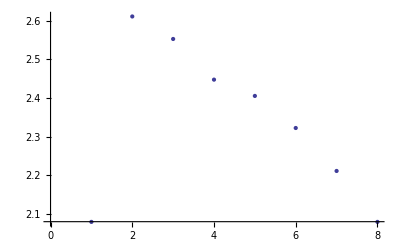

```mathematica
ListPlot[minscores[8]]
```

指標3

```mathematica
minscores3[8]={clusteringAdequationS2[{rt8}]//Log//N,clusteringAdequationS2[cl[8][2]]//Log//N,1.5947961307243337,clusteringAdequationS2[cl[8][4]]//Log//N,clusteringAdequationS2[cl[8][2,2,2,1,1]]//Log//N,clusteringAdequationS2[cl[8][1,1,2,1,1,2]]//Log//N,clusteringAdequationS2[cl[8][7]]//Log//N,clusteringAdequationS2[cl[8][8]]//Log//N}
```

{2.07944,1.68531,1.5948,1.65155,1.77686,1.88821,1.98839,2.07944}

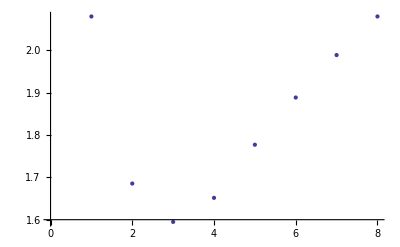

```mathematica
ListPlot[minscores3[8]]
```

## テスト13 指標1 (2D,M:many-sq,1cl,)

```mathematica
li[2,100]=Table[{Random[],Random[]},{100}];
```

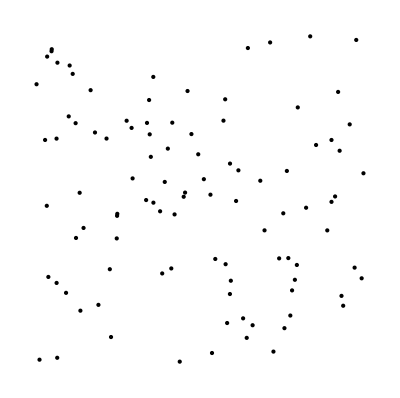

```mathematica
Graphics[Map[Point[#]&,li[2,100]]]
```

```mathematica
clusteringAdequationS[{li[2,100]}]
```

100.

```mathematica
clusteringAdequationS[Map[{#}&,li[2,100]]]
```

100.

```mathematica
(li[2,100,2]=Flatten[{li[2,100],li[2,100]},1])//Length
```

200

```mathematica
clusteringAdequationS[{li[2,100,2]}]
```

200.

```mathematica
clusteringAdequationS[{{{1,1},{2,2},{1,1},{2,2}}}]
```

4

```mathematica
clusteringAdequationS[{{{1,1}},{{2,2}},{{1,1}},{{2,2}}}]
```

4

```mathematica
clusteringAdequationS[{{{1,1},{1,1},{1,1},{2,2},{2,2}}}]
```

5

```mathematica
FindClusters[li[2,100]]
```

{{{0.33541,0.739266},{0.915798,0.197376},{0.772889,0.274267},{0.00861687,0.853905},{0.41696,0.46807},{0.868706,0.420699},{0.410193,0.739976},{0.341611,0.807114},{0.22897,0.104588},{0.572462,0.146131},{0.28982,0.724434},{0.0400206,0.935848},{0.95441,0.985168},{0.124223,0.738472},{0.181521,0.7109},{0.115606,0.884567},{0.764561,0.24283},{0.2469,0.463868},{0.354367,0.502854},{0.905289,0.656753},{0.125397,0.398266},{0.332827,0.510622},{0.835577,0.673833},{0.292806,0.574774},{0.881168,0.688665},{0.168584,0.836302},{0.699647,0.977764},{0.0529776,0.951735},{0.935087,0.734934},{0.806078,0.487867},{0.580719,0.232079},{0.900789,0.831114},{0.455323,0.833813},{0.567962,0.320492},{0.619745,0.159981},{0.275156,0.745718},{0.738578,0.471316},{0.106572,0.909416},{0.0389304,0.493551},{0.0535949,0.957681},{0.103844,0.758617},{0.247517,0.469814},{0.523124,0.526538},{0.346728,0.6387},{0.067802,0.692725},{0.778765,0.318208},{0.448057,0.532744},{0.50361,0.57249},{0.709479,0.0614284},{0.397037,0.663074},{0.670549,0.567877},{0.343442,0.705393},{0.566705,0.80926},{0.0959252,0.235579},{0.0435805,0.282722},{0.749197,0.596879},{0.975778,0.589997},{0.970432,0.278671},{0.527722,0.0572524},{0.466822,0.706181},{0.818243,0.995824},{0.0697852,0.0431067},{0.147694,0.427947},{0.726343,0.337714},{0.580989,0.618687},{0.630418,0.102135},{0.537408,0.335966},{0.88122,0.505257},{0.56163,0.745969},{0.910789,0.226586},{0.0339081,0.688717},{0.443966,0.520406},{0.215666,0.692893},{0.374181,0.477299},{0.0679718,0.264946},{0.647838,0.139585},{0.486983,0.646258},{0.0174203,0.0374495},{0.949575,0.310292},{0.1362,0.532193},{0.387945,0.564323},{0.225411,0.305606},{0.354037,0.875606},{0.781445,0.7852},{0.138371,0.182714},{0.407264,0.307901},{0.0703994,0.917768},{0.759426,0.168316},{0.583416,0.271509},{0.742005,0.130867},{0.633842,0.961217},{0.605806,0.598674},{0.245897,0.396894},{0.380394,0.293068},{0.89186,0.521287},{0.598949,0.507868},{0.753489,0.338574},{0.191686,0.199966},{0.683089,0.420806},{0.43226,0.0316497}}}

```mathematica
1-1/(E^E)//N
```

0.934012

```mathematica
1-1/(E^(E^0))//N
```

0.632121